```mathematica
ForceVec:=Flatten[{Sin[w*t],ConstantArray[0,99]}];

RunLinSysForHarmonicExcitation:=(
System[SetStdParams];
System[SymbolicPrecision]=12;
System[SetStdSysLin];
System[FftMaxFreq]=1.5*N[w/2*π];
System[SetExtExcToPrim];
System[Q]=ForceVec;
System[TIME]=5000;
System[SolveSystem];
System[PrepareGraphs];

{System[graph[3]],System[graph[4]],System[graph[5]],System[graph[6]]} 

)

RunOptSysForHarmonicExcitation:=(
System[SetStdParams];
System[SymbolicPrecision]=12;
System[SetStdSysOpt];
System[FftMaxFreq]=w;
System[SetExtExcToPrim];
System[Q]=ForceVec;
System[TIME]=5000;
System[SolveSystem];
System[PrepareGraphs];

{System[graph[3]],System[graph[4]],System[graph[5]],System[graph[6]]} 
)
```

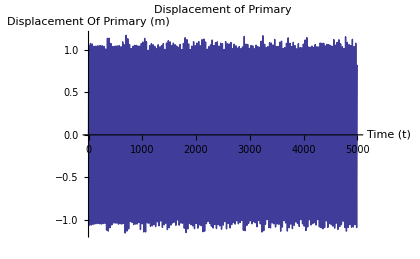
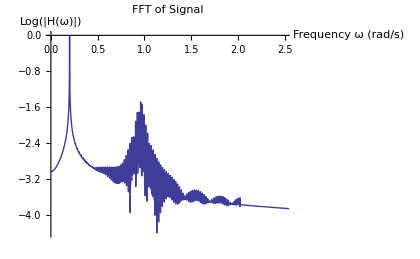
(-Graphics-
-Graphics-
-Graphics3D-
-Graphics3D-)

/Users/Gediz/Desktop/L0.2.jpg

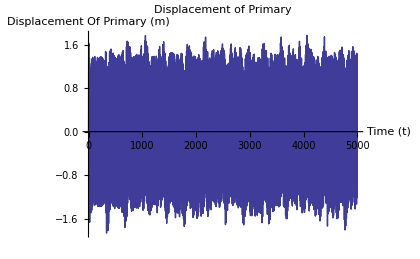
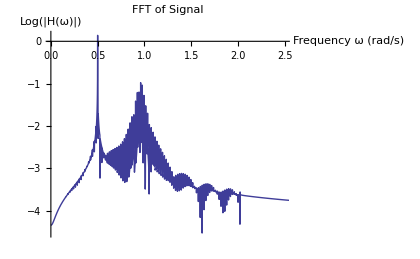
(-Graphics-
-Graphics-
-Graphics3D-
-Graphics3D-)

/Users/Gediz/Desktop/L0.5.jpg

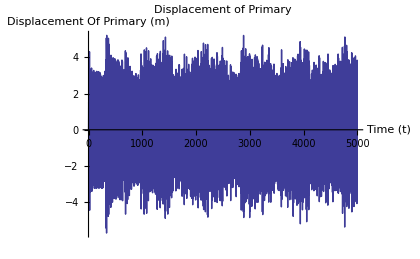
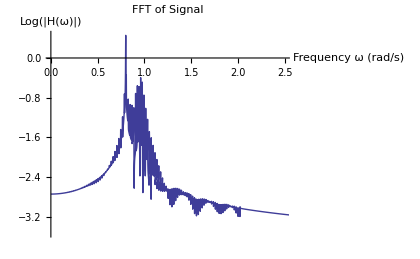
(-Graphics-
-Graphics-
-Graphics3D-
-Graphics3D-)

/Users/Gediz/Desktop/L0.8.jpg

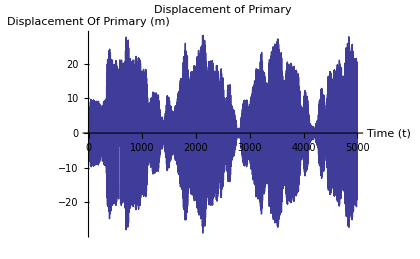
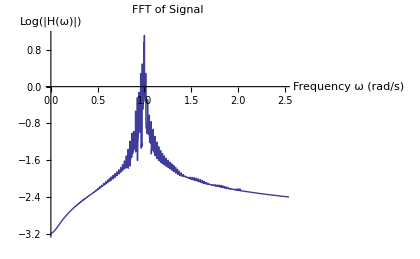
(-Graphics-
-Graphics-
-Graphics3D-
-Graphics3D-)

/Users/Gediz/Desktop/L1.jpg

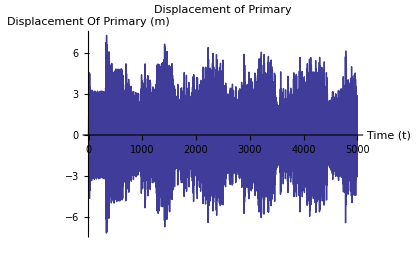
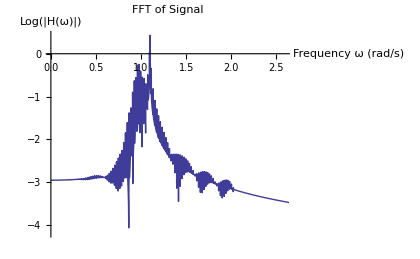
(-Graphics-
-Graphics-
-Graphics3D-
-Graphics3D-)

/Users/Gediz/Desktop/L1.1.jpg

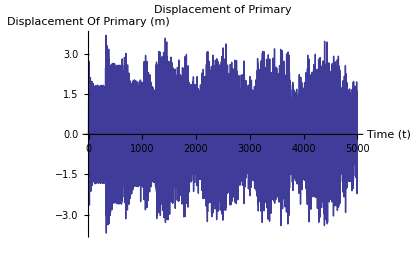
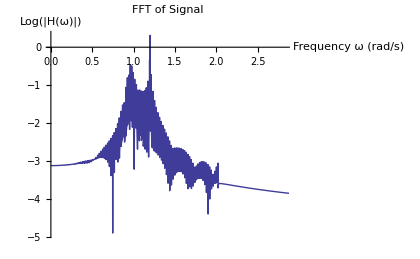
(-Graphics-
-Graphics-
-Graphics3D-
-Graphics3D-)

/Users/Gediz/Desktop/L1.2.jpg

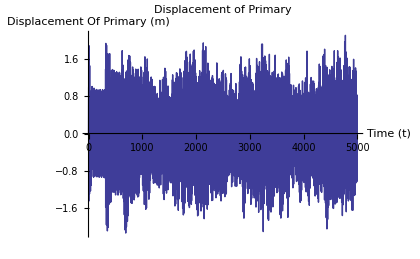
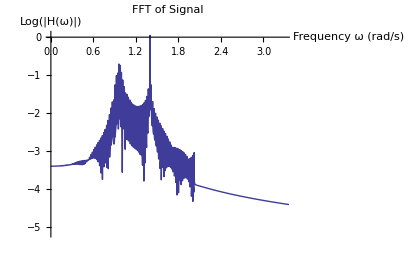
(-Graphics-
-Graphics-
-Graphics3D-
-Graphics3D-)

/Users/Gediz/Desktop/L1.4.jpg

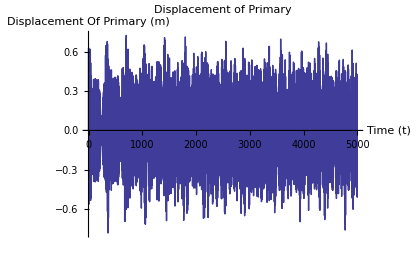
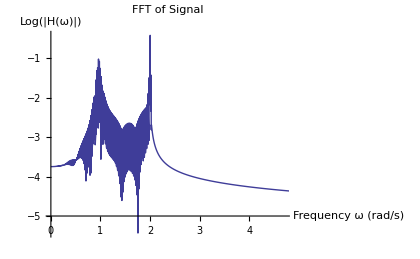
(-Graphics-
-Graphics-
-Graphics3D-
-Graphics3D-)

/Users/Gediz/Desktop/L2.jpg

```mathematica
w=0.2;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=0.5;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=0.8;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=1;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=1.1;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=1.2;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=1.4;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=2;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=5;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
w=0.2;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=0.5;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=0.8;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=1;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=1.1;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=1.2;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=1.4;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=2;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=5;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]

w=10;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=10;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]

w=20;
RunOptSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/O",ToString[w],".jpg"],%,ImageResolution->150]
w=20;
RunLinSysForHarmonicExcitation//MatrixForm
Export[StringJoin["/Users/Gediz/Desktop/L",ToString[w],".jpg"],%,ImageResolution->150]
```